## 基本运算

```mathematica
10! (*注意要在英文状态下输入*）
```

3628800

```mathematica
717/4
```

717/4

```mathematica
N[718/3]
```

239.333

WolframAlphaQueryParseResults   (*这种输入计算方法需要链接网络使用*）

```mathematica
718/3
```

```mathematica
N[718/3,7](*第二个参数是有效数字个数*）
```

```mathematica
239.3333333333333333333`7.
RealDigits[718/3](*repeating decimal  循环小数*)
```

239.3333

{{2,3,9,{3}},3}

```mathematica
a =5
```

5

```mathematica
3a+1
```

16

(*清除〃的变量定义，将〃置于无定义状态.此刻a的颜色变成蓝色，表明没有赋值*）

```mathematica
Clear[a]
```

## 方程组运算

(*展开代数表达式(〃+5)(〃+9) *）

```mathematica
Expand[(a+5) (a+9)]
```

45+14 a+a^2

解关于%的方程2% —7 = 0.

```mathematica
Solve[2x -7 == 0 ,x ]
```

{{x→7/2}}

```mathematica
NSolve[2x-7==0,x]
```

{{x→3.5}}

WolframAlphaQueryResults

WolframAlpha::timeout: 对 WolframAlpha[ solve 2x-7=0,WolframParse] 的调用已经超过了 30. 秒. 增加 TimeConstraint 选项的值可能会改善结果.

x==7/2

```mathematica
Solve[{2 x-7==0,3 x-2y==0},{x,y}]
```

{{x→7/2,y→21/4}}

```mathematica
Solve[a*x^2+b*x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

## 绘制图形

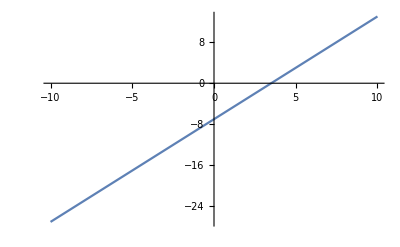

```mathematica
Plot[2x-7,{x,-10,10}] (*绘制方程y=2%-7,其中％从一10到10.*)
```

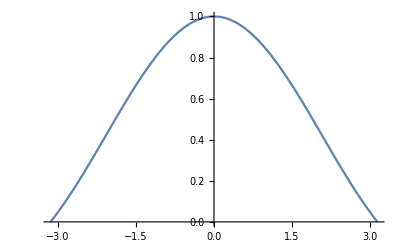

```mathematica
Plot [Sin[X]/X,{X,- Pi,Pi}] (*绘制sin(x)/x,其中％从-pi 到 pi*)
```

WolframAlphaQueryParseResults

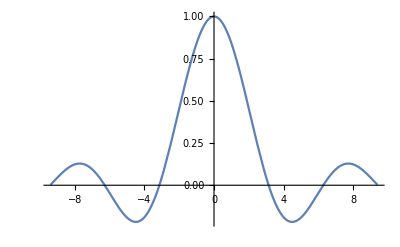

```mathematica
Plot3D[Sin[x*y],{x,-3,3},{y,-5,5}]  (*在三维空间绘制sin(%))，其中无从-3到3,7从-5到5 *)
```

-Graphics3D-

WolframAlphaQueryParseResults

-Graphics3D-

## 列表

```mathematica
Table[i^2, {i, 1, 5}](*列表生成式 *)
```

{1,4,9,16,25}

符号%表示上一次计算或上一个输出单元.请注意是被执行过的上一次计算，不一
定是紧挨着新计算的上一个计算

```mathematica
Total[%]
```

55

在Wolfram语一 言中也有Sum指令，但用于数学求和运算，需要提供参数作为索弓I.如果像上一个例子一样，数值列表已经存在，那么应该用Total指令来求它们的和.

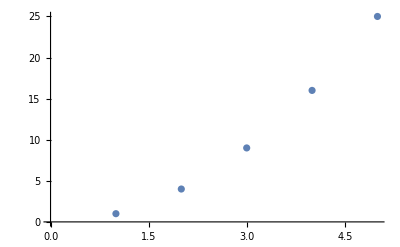

```mathematica
ListPlot[Table[i^2,{i,1,5}]]
```

```mathematica
matl={{1,2,3},{3,5,7},{4,6,8}};(*,它是由三个子列表组成的列表，在语句末尾加上分号抑制输出.*)
```

在MATHEMATICA 中，列表于其子列表组成的二维列表被认为是矩阵

```mathematica
Det[matl]
```

0

## 积分

```mathematica
lntegrate[Sin[x],x] (*计算sin(x)关于x的不定积分.*)
```

lntegrate[Sin[x],x]

WolframAlphaQueryParseResults

-Cos[x]

WolframAlphaQueryResults

80.1 yr

```mathematica
CountryData["UnitedStates","LifeExpectancy"]
```

80.1 yr

```mathematica
QuantityForm[Quantity[80.1,"Years"],"Abbreviation"]
```

80.1 yr

Delete Cases指令用于将一个或者多个数值缺失的数据删除
变量包括国家名称和相应预期寿命的数据组

```mathematica
data=DeleteCases[Table[{i,CountryData[i,"LifeExpectancy"]},{i,CountryData[All]}]{_,_Missing}];
```

Thread::tdlen: … 中长度不相等的对象无法合并.

```mathematica
Short[data]
```

DeleteCases[{_,_Missing} {{Afghanistan,52.1 yr},{Aland Islands,Missing[NotAvailable]},{Albania,78.6 yr},{Algeria,77.2 yr},{American Samoa,73.9 yr},{Andorra,82.9 yr},{Angola,60.6 yr},{Anguilla,81.6 yr},{Antigua and Barbuda,76.9 yr},{Argentina,77.5 yr},{Armenia,75.1 yr},{Aruba,77.1 yr},{Australia,82.4 yr},{Austria,81.7 yr},«222»,{United States Virgin Islands,79.5 yr},{Uruguay,77.6 yr},{Uzbekistan,74.3 yr},{Vanuatu,74. yr},{Vatican City,Missing[NotAvailable]},{Venezuela,76.2 yr},{Vietnam,73.9 yr},{Wallis and Futuna Islands,80. yr},{West Bank,75.4 yr},{Western Sahara,63.8 yr},{Yemen,66.2 yr},{Zambia,53. yr},{Zimbabwe,61.1 yr}}]

```mathematica
(* 如SortBy函数可对列表按预期寿命从低到高排序. *)
Short[SortBy[data,Last]]
```

DeleteCases[{_,_Missing} {{Afghanistan,52.1 yr},{Aland Islands,Missing[NotAvailable]},{Albania,78.6 yr},{Algeria,77.2 yr},{American Samoa,73.9 yr},{Andorra,82.9 yr},{Angola,60.6 yr},{Anguilla,81.6 yr},{Antigua and Barbuda,76.9 yr},{Argentina,77.5 yr},{Armenia,75.1 yr},{Aruba,77.1 yr},{Australia,82.4 yr},{Austria,81.7 yr},«222»,{United States Virgin Islands,79.5 yr},{Uruguay,77.6 yr},{Uzbekistan,74.3 yr},{Vanuatu,74. yr},{Vatican City,Missing[NotAvailable]},{Venezuela,76.2 yr},{Vietnam,73.9 yr},{Wallis and Futuna Islands,80. yr},{West Bank,75.4 yr},{Western Sahara,63.8 yr},{Yemen,66.2 yr},{Zambia,53. yr},{Zimbabwe,61.1 yr}}]

```mathematica
CountryData
```

CountryData

```mathematica
CountryData[all]
```

CountryData::notent: all 不是 CountryData 的一个已知实体、类别或者标签. 请使用 CountryData[] 以获取实体列表.

WolframAlphaQueryNoResults

WolframAlphaQueryParseResults

WolframAlphaQueryNoResults

```mathematica
Histogram[data[All,2]]
```

DeleteCases::argx: 调用 … 时使用了 2 个参数；应该用 1 个参数.

Histogram::ldata: «1» 不是一个有效的数据集或者数据集列表.

Histogram[DeleteCases[{_,_Missing} {{Afghanistan,52.1 yr},{Aland Islands,Missing[NotAvailable]},{Albania,78.6 yr},{Algeria,77.2 yr},{American Samoa,73.9 yr},{Andorra,82.9 yr},{Angola,60.6 yr},{Anguilla,81.6 yr},{Antigua and Barbuda,76.9 yr},{Argentina,77.5 yr},{Armenia,75.1 yr},{Aruba,77.1 yr},{Australia,82.4 yr},{Austria,81.7 yr},{Azerbaijan,73. yr},{Bahamas,72.9 yr},{Bahrain,79.1 yr},{Bangladesh,73.7 yr},{Barbados,75.7 yr},{Belarus,73.2 yr},{Belgium,81.2 yr},{Belize,74.7 yr},{Benin,62.7 yr},{Bermuda,81.5 yr},{Bhutan,71.1 yr},{Bolivia,69.8 yr},{Caribbean Netherlands,Missing[NotAvailable]},{Bosnia and Herzegovina,77.1 yr},{Botswana,63.8 yr},{Bouvet Island,Missing[NotAvailable]},{Brazil,74.3 yr},{British Indian Ocean Territory,Missing[NotAvailable]},{British Virgin Islands,78.9 yr},{Brunei,77.5 yr},{Bulgaria,74.8 yr},{Burkina Faso,61.8 yr},{Burundi,61.4 yr},{Cambodia,65.2 yr},{Cameroon,59.4 yr},{Canada,82. yr},{Cape Verde,72.7 yr},{Cayman Islands,81.4 yr},{Central African Republic,53.3 yr},{Chad,57.5 yr},{Chile,79.1 yr},{China,75.8 yr},{Christmas Island,Missing[NotAvailable]},{Cocos Keeling Islands,Missing[NotAvailable]},{Colombia,76.2 yr},{Comoros,64.9 yr},{Cook Islands,76.2 yr},{Costa Rica,78.9 yr},{Croatia,76.3 yr},{Cuba,78.9 yr},{Curacao,78.6 yr},{Cyprus,79. yr},{Czech Republic,78.9 yr},{Democratic Republic of the Congo,58.1 yr},{Denmark,81. yr},{Djibouti,64. yr},{Dominica,77.4 yr},{Dominican Republic,71.3 yr},{East Timor,68.7 yr},{Ecuador,77.1 yr},{Egypt,73.2 yr},{El Salvador,75.1 yr},{Equatorial Guinea,65. yr},{Eritrea,65.6 yr},{Estonia,77. yr},{Ethiopia,65.475 yr},{Falkland Islands,Missing[NotAvailable]},{Faroe Islands,80.6 yr},{Fiji,73.2 yr},{Finland,81.1 yr},{France,82. yr},{French Guiana,77.121 yr},{French Polynesia,77.5 yr},{French Southern And Antarctic lands,Missing[NotAvailable]},{Gabon,68. yr},{Gambia,65.4 yr},{Gaza Strip,74.4 yr},{Georgia,76.6 yr},{Germany,80.9 yr},{Ghana,67.4 yr},{Gibraltar,79.7 yr},{Greece,80.8 yr},{Greenland,72.9 yr},{Grenada,74.8 yr},{Guadeloupe,80.947 yr},{Guam,76.4 yr},{Guatemala,71.8 yr},{Guernsey,82.7 yr},{Guinea,62.1 yr},{Guinea-Bissau,61.4 yr},{Guyana,68.9 yr},{Haiti,64.6 yr},{Honduras,71.3 yr},{Hong Kong,83.1 yr},{Hungary,76.3 yr},{Iceland,83.1 yr},{India,69.1 yr},{Indonesia,73.2 yr},{Iran,74.2 yr},{Iraq,74.9 yr},{Ireland,81. yr},{Isle of Man,81.4 yr},{Israel,82.7 yr},{Italy,82.4 yr},{Ivory Coast,60.1 yr},{Jamaica,74.5 yr},{Japan,85.5 yr},{Jersey,82. yr},{Jordan,75. yr},{Kazakhstan,71.4 yr},{Kenya,64.6 yr},{Kiribati,66.9 yr},{Kosovo,71.6463 yr},{Kuwait,78.3 yr},{Kyrgyzstan,71.2 yr},{Laos,65. yr},{Latvia,74.9 yr},{Lebanon,77.9 yr},{Lesotho,53. yr},{Liberia,63.8 yr},{Libya,76.9 yr},{Liechtenstein,82. yr},{Lithuania,75.2 yr},{Luxembourg,82.4 yr},{Macau,84.6 yr},{North Macedonia,75.9 yr},{Madagascar,66.6 yr},{Malawi,62.2 yr},{Malaysia,75.4 yr},{Maldives,76. yr},{Mali,60.8 yr},{Malta,82.7 yr},{Marshall Islands,73.6 yr},{Martinique,81.41 yr},{Mauritania,63.8 yr},{Mauritius,76. yr},{Mayotte,79.19 yr},{Mexico,76.3 yr},{Micronesia,73.4 yr},{Moldova,71.3 yr},{Monaco,89.4 yr},{Mongolia,70.2 yr},{Montenegro,77.116 yr},{Montserrat,74.8 yr},{Morocco,77.3 yr},{Mozambique,54.1 yr},{Myanmar,68.6 yr},{Namibia,64.4 yr},{Nauru,67.8 yr},{Nepal,71.3 yr},{Netherlands,81.5 yr},{New Caledonia,78. yr},{New Zealand,81.4 yr},{Nicaragua,73.7 yr},{Niger,56.3 yr},{Nigeria,59.3 yr},{Niue,Missing[NotAvailable]},{Norfolk Island,Missing[NotAvailable]},{Northern Mariana Islands,75.6 yr},{North Korea,71. yr},{Norway,82. yr},{Oman,75.9 yr},{Pakistan,68.4 yr},{Palau,73.6 yr},{Panama,78.9 yr},{Papua New Guinea,67.5 yr},{Paraguay,77.6 yr},{Peru,74.2 yr},{Philippines,69.6 yr},{Pitcairn Islands,Missing[NotAvailable]},{Poland,77.9 yr},{Portugal,80.9 yr},{Puerto Rico,81. yr},{Qatar,79. yr},{Republic of the Congo,60.3 yr},{Réunion,79.646 yr},{Romania,75.6 yr},{Russia,71.3 yr},{Rwanda,64.5 yr},{Saint Barthelemy,Missing[NotAvailable]},{Saint Helena, Ascension and Tristan da Cunha,79.8 yr},{Saint Kitts and Nevis,76.2 yr},{Saint Lucia,78.1 yr},{Saint Martin,79.622 yr},{Saint Pierre and Miquelon,80.7 yr},{Saint Vincent and the Grenadines,75.8 yr},{Samoa,74.2 yr},{San Marino,83.4 yr},{São Tomé and Príncipe,65.7 yr},{Saudi Arabia,75.7 yr},{Senegal,62.5 yr},{Serbia,75.9 yr},{Seychelles,75.2 yr},{Sierra Leone,59. yr},{Singapore,85.5 yr},{Sint Maarten,78.5 yr},{Slovakia,77.4 yr},{Slovenia,81.2 yr},{Solomon Islands,75.8 yr},{Somalia,53.2 yr},{South Africa,64.1 yr},{South Georgia and the South Sandwich Islands,Missing[NotAvailable]},{South Korea,82.5 yr},{South Sudan,56.811 yr},{Spain,81.8 yr},{Sri Lanka,77.1 yr},{Sudan,65.8 yr},{Suriname,72.8 yr},{Svalbard,Missing[NotAvailable]},{Eswatini,57.754 yr},{Sweden,82.2 yr},{Switzerland,82.7 yr},{Syria,75.2 yr},{Taiwan,80.4 yr},{Tajikistan,68.4 yr},{Tanzania,63.1 yr},{Thailand,75.1 yr},{Togo,65.8 yr},{Tokelau,Missing[NotAvailable]},{Tonga,76.6 yr},{Trinidad and Tobago,73.4 yr},{Tunisia,75.9 yr},{Turkey,75.3 yr},{Turkmenistan,70.7 yr},{Turks and Caicos Islands,80.1 yr},{Tuvalu,67.2 yr},{Uganda,56.3 yr},{Ukraine,72.4 yr},{United Arab Emirates,78.7 yr},{United Kingdom,80.9 yr},{United States,80.1 yr},{United States Minor Outlying Islands,Missing[NotAvailable]},{United States Virgin Islands,79.5 yr},{Uruguay,77.6 yr},{Uzbekistan,74.3 yr},{Vanuatu,74. yr},{Vatican City,Missing[NotAvailable]},{Venezuela,76.2 yr},{Vietnam,73.9 yr},{Wallis and Futuna Islands,80. yr},{West Bank,75.4 yr},{Western Sahara,63.8 yr},{Yemen,66.2 yr},{Zambia,53. yr},{Zimbabwe,61.1 yr}}][All,2]]

```mathematica
dataAfrica= DeleteCases[Table[{i,CountryData[i,"LifeExpectancy"]},{i,CountryData["Asia"]}],{
_,_Missing}]
```

```mathematica
dataAfrica=DeleteCases[Table[{i,CountryDatafi,HLifeExpectancyn]},{i,CountryData[nAfrica1']}],J,—Missing}];
Mean[dataAfrica[All,2]]
```